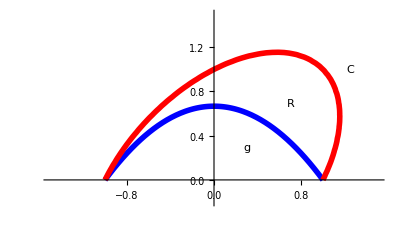

```mathematica
x[t_]=t;
y[t_]=-2t^2/3+2/3;
a=ParametricPlot[{x[t],y[t]},{t,-1,1},PlotStyle->{Thickness[.01],Blue}];
b=ContourPlot[x^2+y^2-x y ==1,{x,-1.5,1.5},{y,0,1.5},ContourStyle->{Thickness[.01],Red}];
words=Graphics[{Text["R",{.7,.7},BaseStyle->{FontSlant->"Italics",FontFamily->"Times",FontSize->30}],Text["C",{1.25,1},BaseStyle->{Red,FontSlant->"Italics",FontFamily->"Times",FontSize->30}],
Text["g",{.3,.3},BaseStyle->{Blue,FontWeight->"Bold",FontFamily->"Times",FontSize->30}]}
];
Show[a,b,words,PlotRange->{{-1.5,1.5},{-.2,1.5}}]
```

```mathematica
Solve[x'[t]-y'[t]==0,t]
```

{{t→-3/4}}

```mathematica
y[-3/4]
```

7/24

```mathematica
1/Sqrt[3.]
```

0.57735